```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/zeno/Documents/MPI_DIS

```mathematica
Get["/Users/zeno/Applications/package-x-root/X/Kernel/init.m"]
```

Package-X v2.1.1 [patched 22/08/2020], by Hiren H. Patel
For more information, see the

All expressions in this notebook match the conventions of Package X, as given in[arXiv : 1612.00009] . Package X can be downloaded from https://gitlab.com/mule-tools/package-x .

```mathematica
SP[v_,w_]:=v[[1]]w[[1]]-v[[2]]w[[2]]-v[[3]]w[[3]]-v[[4]]w[[4]]
```

```mathematica
norm3D[v_]:=Sqrt[v[[1]]^2+v[[2]]^2+v[[3]]^2]
```

```mathematica
vec[w_]:={w[[2]],w[[3]],w[[4]]}
```

```mathematica
ClearAll[p1,p2,p3,p4]
```

```mathematica
esurf[k_,p1_,p2_]:=norm3D[k+vec[p1]]+norm3D[k+vec[p2]]-p2[[1]]+p1[[1]];
```

```mathematica
zerovec={0,0,0,0};
```

## Triangles

First benchmarks are associated with the triangle diagram with massless internal propagators, varying external masses and varying numerator. With this setup, the triangle diagram is a function of three scales,   , and reads:

We can’t test IR subtraction with triangles, since the triangle is the essential unit for the subtraction of all one-loop integrals. However, we can test integration in the euclidean region, in the physical region, the correct implementation of numerators, as well as UV subtraction.

#### First example: no numerator, no UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p2,0}]]]/.{p1.p2->1/2(p3.p3-p1.p1-p2.p2)}
```

-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//N//Simplify]
```

-4.36934+0. ⅈ

```mathematica
p1sq=1/4;
p2sq=2/3;
p3sq=1;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]
```

4.0704-6.83439×10^-17 ⅈ

#### Second example: numerator, no UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[p1.k,k,{k,0},{k+p1,0},{k-p2,0}]]]/.{p1.p2->1/2(p3.p3-p1.p1-p2.p2)}
```

1/2 Log[-µ^2/(p2.p2)]-1/2 Log[-µ^2/(p3.p3)]-1/2 p1.p1 (-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1+p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)/(-√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p3.p3]-p1.p1+p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,p3.p3]+p1.p1-p2.p2-p3.p3)]/(√Kallenλ[p1.p1,p2.p2,p3.p3]))

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]
```

-1.40664+0. ⅈ

```mathematica
p1sq=1/4;
p2sq=2/3;
p3sq=1;
```

```mathematica
Assuming[ µ>0,result/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]
```

-0.306067+8.54299×10^-18 ⅈ

#### Third example: numerator, UV, physical and euclidean

```mathematica
result=C0Expand[LoopRefine[LoopIntegrate[p1.k p2.k,k,{k,0},{k+p1,0},{k+p2,0}]]]
```

(p1.p2)/2+(p1.p2)/(4 ϵ)-1/4 p1.p1 Log[-µ^2/(p1.p1)]-1/4 p2.p2 Log[-µ^2/(p2.p2)]+1/4 (p1.p1+p1.p2+p2.p2) Log[-µ^2/(p1.p1-2 p1.p2+p2.p2)]+1/4 p1.p1 p2.p2 (-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)/(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p1-2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)/(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])-PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2])+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]-2 p1.p2+2 p2.p2)/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]+2 p1.p2-2 p2.p2)]/(√Kallenλ[p1.p1,p2.p2,p1.p1-2 p1.p2+p2.p2]))

The diagram has a UV pole. We can construct a counter-term:

```mathematica
counterterm=LoopRefine[LoopIntegrate[p1.k p2.k,k,{k,muv},{k,muv},{k,muv}]]
```

1/4 p1.p2 (1/ϵ+Log[µ^2/muv^2])

The diagram minus the counter-term evaluates to a finite quantity now:

```mathematica
subtractedresult=result-counterterm/.{p1.p2->1/2(p3.p3-p1.p1-p2.p2)}//Simplify
```

1/8 (p3.p3 (2-Log[µ^2/muv^2]+Log[-µ^2/(2 p1.p1+2 p2.p2-p3.p3)])+p2.p2 (-2+Log[µ^2/muv^2]-2 Log[-µ^2/(p2.p2)]+Log[-µ^2/(2 p1.p1+2 p2.p2-p3.p3)])+p1.p1 (-2+Log[µ^2/muv^2]-2 Log[-µ^2/(p1.p1)]+Log[-µ^2/(2 p1.p1+2 p2.p2-p3.p3)]+(2 p2.p2 (PolyLog[2,(-√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+p1.p1+p2.p2-p3.p3)]+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+p1.p1+3 p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]-p1.p1-3 p2.p2+p3.p3)]-PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]-p1.p1-3 p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+p1.p1+3 p2.p2-p3.p3)]+PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+3 p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]-3 p1.p1-p2.p2+p3.p3)]-PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]-3 p1.p1-p2.p2+p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+3 p1.p1+p2.p2-p3.p3)]-PolyLog[2,-(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]+p1.p1+p2.p2-p3.p3)/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3]-p1.p1-p2.p2+p3.p3)]))/(√Kallenλ[p1.p1,p2.p2,2 p1.p1+2 p2.p2-p3.p3])))

```mathematica
p1sq=-1/2;
p2sq=-3/4;
p3sq=-2/5;
muv=1;
```

```mathematica
Assuming[ µ>0,subtractedresult/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]
```

0.280378+0. ⅈ

```mathematica
p1sq=1/4;
p2sq=2/3;
p3sq=1;
```

```mathematica
Assuming[ µ>0,subtractedresult/.{p1.p1->p1sq,p2.p2->p2sq,p3.p3->p3sq}//PowerExpand//Simplify//N]
```

0.0921444+0.0327249 ⅈ

## Boxes

The second set of benchmarks concerns the box diagram with vanishing internal masses, varying external masses and varying numerator. With this setup, the box diagram is a function of six invariants. Contrary to the triangle, we now derive the invariants from explicit values of four-momenta for the external particles, for ease of execution. The diagram reads

We can now test IR and UV subtraction and the correct implementation of numerators in the euclidean and physical regime.

### Finite boxes in physical region

We start with finite boxes. While for the triangle there is always a frame in which all E-surfaces admit a single center, this is not the case for the boxes. We should a challenging physical point with multiple overlaps, for example:

```mathematica
p1phys={0.99,0,0.96,0};
p2phys={0.82,0.65,0.,0};
p4phys={-0.71,-0.45,-0.53,0};
p3phys=-p1phys-p2phys-p4phys;
```

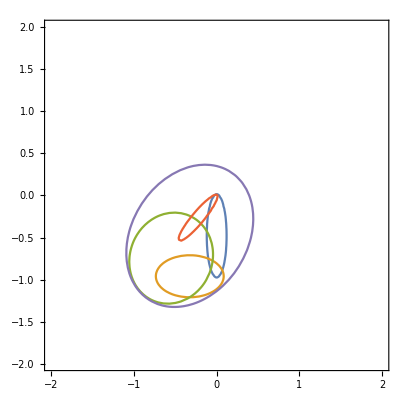

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys]==0,esurf[{kx,ky,0},p1phys,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys+p2phys+p3phys,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys+p2phys+p3phys+p4phys,p1phys+p2phys+p3phys]==0,esurf[{kx,ky,0},zerovec,p1phys+p2phys]==0,esurf[{kx,ky,0},p1phys,p1phys+p2phys+p3phys]==0},{kx,-2,2},{ky,-2,2}]
```

#### First example: no numerator

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]]]
```

ConditionalExpression[ScalarC0[p2.p2 p4.p4,(p1.p1+2 p1.p2+p2.p2) (p1.p1+2 p1.p4+p4.p4),p1.p1 (p1.p1+2 p1.p2+2 p1.p4+p2.p2+2 p2.p4+p4.p4),0,0,0], ]

```mathematica
p1sq=SP[p1phys,p1phys];
p2sq=SP[p2phys,p2phys];
p4sq=SP[p4phys,p4phys];
p1p4=SP[p1phys,p4phys];
p1p2=SP[p1phys,p2phys];
p2p4=SP[p2phys,p4phys];
```

```mathematica
C0Expand[result/.{p1.p1->p1sq,p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}]
```

-7.93527-34.7353 ⅈ

#### Second example: numerator

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[k.p1 k.p2 k.p4,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]]];
```

```mathematica
p1sq=SP[p1phys,p1phys];
p2sq=SP[p2phys,p2phys];
p4sq=SP[p4phys,p4phys];
p1p4=SP[p1phys,p4phys];
p1p2=SP[p1phys,p2phys];
p2p4=SP[p2phys,p4phys];
```

```mathematica
Assuming[ µ>0,C0Expand[result/.{p1.p1->p1sq,p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}]//PowerExpand//Simplify//N]
```

(0.467305-0.361178 ⅈ)-8.32667×10^-17 Log[µ]

### Divergent boxes

We need to cook up a bunch of IR-singular momentum configurations for the external legs.

1) Euclidean, one massless external:

```mathematica
p1unphys1os={1,0,1,0};
p2unphys1os={-0.2,0.65,0.,0};
p4unphys1os={-0.71,-0.45,-0.53,-0.4};
p3unphys1os=-p1unphys1os-p2unphys1os-p4unphys1os;
```

```mathematica
{SP[p1unphys1os,p1unphys1os],
SP[p2unphys1os,p2unphys1os],
SP[p3unphys1os,p3unphys1os],
SP[p4unphys1os,p4unphys1os],
SP[p1unphys1os+p2unphys1os,p1unphys1os+p2unphys1os],
SP[p1unphys1os+p4unphys1os,p1unphys1os+p4unphys1os]}
```

{0,-0.3825,-0.4128,-0.1393,-0.7825,-0.4993}

2) Euclidean, two massless externals

```mathematica
p1unphys2os={1,0,1,0};
p2unphys2os={-1,1,0.,0};
p4unphys2os={-0.71,-0.45,-0.53,-0.4};
p3unphys2os=-p1unphys2os-p2unphys2os-p4unphys2os;
```

```mathematica
{SP[p1unphys2os,p1unphys2os],
SP[p2unphys2os,p2unphys2os],
SP[p3unphys2os,p3unphys2os],
SP[p4unphys2os,p4unphys2os],
SP[p1unphys2os+p2unphys2os,p1unphys2os+p2unphys2os],
SP[p1unphys2os+p4unphys2os,p1unphys2os+p4unphys2os]}
```

{0,0.,-0.1793,-0.1393,-2.,-0.4993}

3) Physical, one massless external

```mathematica
p1phys1os={1,0,1,0};
p2phys1os={0.82,0.45,0.,0};
p4phys1os={-0.71,-0.55,-0.23,0};
p3phys1os=-p1phys1os-p2phys1os-p4phys1os;
```

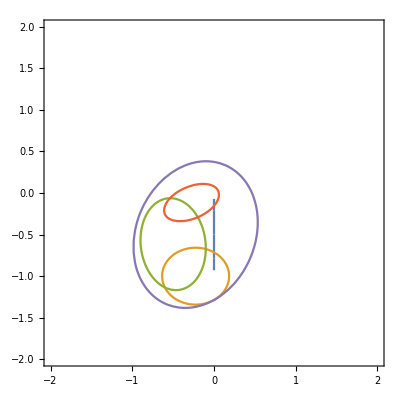

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys1os]==0,esurf[{kx,ky,0},p1phys1os,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os+p2phys1os+p3phys1os,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os+p2phys1os+p3phys1os+p4phys1os,p1phys1os+p2phys1os+p3phys1os]==0,esurf[{kx,ky,0},zerovec,p1phys1os+p2phys1os]==0,esurf[{kx,ky,0},p1phys1os,p1phys1os+p2phys1os+p3phys1os]==0},{kx,-2,2},{ky,-2,2}]
```

4) Physical, two massless externals

```mathematica
p1phys2os={1,0,1,0};
p2phys2os={1,0,-1,0};
p4phys2os={-0.71,-0.45,-0.53,0};
p3phys2os=-p1phys2os-p2phys2os-p4phys2os;
```

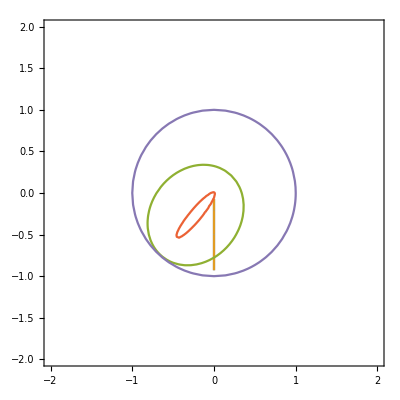

```mathematica
ContourPlot[{esurf[{kx,ky,0},zerovec,p1phys2os]==0,esurf[{kx,ky,0},p1phys2os,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os+p2phys2os+p3phys2os,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os+p2phys2os+p3phys2os+p4phys2os,p1phys2os+p2phys2os+p3phys2os]==0,esurf[{kx,ky,0},zerovec,p1phys2os+p2phys2os]==0,esurf[{kx,ky,0},p1phys2os,p1phys2os+p2phys2os+p3phys2os]==0},{kx,-2,2},{ky,-2,2}]
```

#### IR divergent box: no numerator

We start with case 1)

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
p2sq=SP[p2unphys1os,p2unphys1os];
p4sq=SP[p4unphys1os,p4unphys1os];
p1p4=SP[p1unphys1os,p4unphys1os];
p1p2=SP[p1unphys1os,p2unphys1os];
p2p4=SP[p2unphys1os,p4unphys1os];
```

```mathematica
resultBox1os=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-5.35039-5.90464/ϵ-11.8093 Log[µ]

This box has a collinear singularity, we need to subtract it. We follow the method laid out in [arXiv:1912.09291]. We construct the two triangle integrals obtained by contracting one-by-one the edges of the graph that are hard in the collinear limit:

```mathematica
ctTriangle1=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0}]];
ctTriangle2=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0}]/.{p1.p1->0}]];
```

and we take the linear combination of them that subtracts locally the singularity, which can be obtained by solving a simple linear system

```mathematica
sol=Solve[{2p1.p2 t2 -2 p1.p4 t1==0, 1-t2(2p1.p2+p2.p2)-t1 p4.p4==0},{t1,t2}][[1]]
```

{t1→(p1.p2)/(2 p1.p2 p1.p4+p1.p4 p2.p2+p1.p2 p4.p4),t2→(p1.p4)/(2 p1.p2 p1.p4+p1.p4 p2.p2+p1.p2 p4.p4)}

```mathematica
ctBox1os=C0Expand[(t1 ctTriangle1+t2 ctTriangle2)/.sol];
cteval=Assuming[ µ>0,ctBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-6.32203-5.90464/ϵ-11.8093 Log[µ]

Now the difference between the original integral and the counter-term is finite:

```mathematica
subtractedBox1os=resultBox1os-ctBox1os;
```

```mathematica
subtractedresult=resulteval-cteval//Simplify
```

0.97164+1.77636×10^-15 Log[µ]

We now proceed with case 2)

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
p4sq=SP[p4unphys2os,p4unphys2os];
p1p4=SP[p1unphys2os,p4unphys2os];
p1p2=SP[p1unphys2os,p2unphys2os];
p2p4=SP[p2unphys2os,p4unphys2os];
```

```mathematica
resultBox2os=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-2.45779+1.0014/ϵ^2-2.99807/ϵ+(-5.99614+2.0028/ϵ) Log[µ]+2.0028 Log[µ]^2

Since the box has now two adjacent massless externals, there is now a soft singularity, identified by a double pole. The counter-term is constructed in the same way as before:

```mathematica
ctTriangle1=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
ctTriangle2=C0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k-p4,0}]/.{p1.p1->0,p2.p2->0}]];
ctTriangle3=C0Expand[LoopRefine[LoopIntegrate[1,k,{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
sol=Solve[{2p1.p2 t2 -2 p1.p4 t1==0, 1-t2(2p1.p2)-t1 p4.p4==0,t1==1/(2p1.p4+p4.p4), t1(p1.p2+p2.p4)+t3 p1.p2==0},{t1,t2,t3}][[1]]
```

{t1→-1/(-2 p1.p4-p4.p4),t2→(p1.p4)/(p1.p2 (2 p1.p4+p4.p4)),t3→-(p1.p2+p2.p4)/(p1.p2 (2 p1.p4+p4.p4))}

```mathematica
ctBox2os=C0Expand[(t1 ctTriangle1+t2 ctTriangle2+t3 ctTriangle3)/.sol];
```

```mathematica
cteval=Assuming[ µ>0,ctBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-3.5244+1.0014/ϵ^2-2.99807/ϵ+(-5.99614+2.0028/ϵ) Log[µ]+2.0028 Log[µ]^2

Now the difference is finite

```mathematica
subtractedBox2os=resultBox2os-ctBox2os;
```

```mathematica
subtractedresult=resulteval-cteval//Simplify
```

1.06661-1.33227×10^-15 Log[µ]^2

We can re-use the subtracted boxes we derived to immediately obtain the value at physical points, 3) and 4):

```mathematica
p2sq=SP[p2phys1os,p2phys1os];
p4sq=SP[p4phys1os,p4phys1os];
p1p4=SP[p1phys1os,p4phys1os];
p1p2=SP[p1phys1os,p2phys1os];
p2p4=SP[p2phys1os,p4phys1os];
```

```mathematica
Assuming[ µ>0,resultBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.64086+1.67947 ⅈ)+(1.79531+1.76332 ⅈ)/ϵ+(3.59061+3.52664 ⅈ) Log[µ]

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox1os/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(0.11827-4.32939 ⅈ)-(0.+4.44089×10^-16 ⅈ)/ϵ-(0.+8.88178×10^-16 ⅈ) Log[µ]-2.22045×10^-16 Log[µ]^2

```mathematica
p4sq=SP[p4phys2os,p4phys2os];
p1p4=SP[p1phys2os,p4phys2os];
p1p2=SP[p1phys2os,p2phys2os];
p2p4=SP[p2phys2os,p4phys2os];
```

```mathematica
Assuming[ µ>0,resultBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-0.970603+7.59491 ⅈ)-0.736811/ϵ^2+(2.16333+2.31476 ⅈ)/ϵ+((4.32665+4.62952 ⅈ)-1.47362/ϵ) Log[µ]-1.47362 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox2os/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.92127-4.20529 ⅈ)+(4.44089×10^-16+0. ⅈ)/ϵ-(3.07819×10^-16-6.97574×10^-16 ⅈ) Log[µ]+6.66134×10^-16 Log[µ]^2

#### IR divergent boxes: numerator

We start with the point 1):

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[p4.k,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
p2sq=SP[p2unphys1os,p2unphys1os];
p4sq=SP[p4unphys1os,p4unphys1os];
p1p4=SP[p1unphys1os,p4unphys1os];
p1p2=SP[p1unphys1os,p2unphys1os];
p2p4=SP[p2unphys1os,p4unphys1os];
```

```mathematica
resultBox1osNum=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-2.89532+0. ⅈ)-0.483449/ϵ-0.966897 Log[µ]-3.33067×10^-16 Log[µ]^2

The counter-term is:

```mathematica
ctBox1osNum=1/2(p4.p4)ctBox1os-1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0}]];
```

```mathematica
cteval=Assuming[ µ>0,ctBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-0.0993077-0.483449/ϵ-0.966897 Log[µ]

and the subtracted integrand is finite:

```mathematica
subtractedBox1osNum=resultBox1osNum-ctBox1osNum;
```

```mathematica
Assuming[ µ>0,subtractedBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-2.79601+0. ⅈ)-(5.55112×10^-17)/ϵ+2.22045×10^-16 Log[µ]-1.11022×10^-16 Log[µ]^2

We may now proceed to point 2):

```mathematica
result=D0Expand[LoopRefine[LoopIntegrate[p4.k,k,{k,0},{k+p1,0},{k-p4,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
p4sq=SP[p4unphys2os,p4unphys2os];
p1p4=SP[p1unphys2os,p4unphys2os];
p1p2=SP[p1unphys2os,p2unphys2os];
p2p4=SP[p2unphys2os,p4unphys2os];
```

```mathematica
resultBox2osNum=C0Expand[result];
```

```mathematica
resulteval=Assuming[ µ>0,resultBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

1.9565+0.180252/ϵ^2+1.63576/ϵ+(3.27152+0.360505/ϵ) Log[µ]+0.360505 Log[µ]^2

The counter-term is now given by

```mathematica
ctBox2osNum=1/2(p4.p4)ctBox2os-1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k,0},{k+p1,0},{k+p1+p2,0}]/.{p1.p1->0,p2.p2->0}]]+1/2D0Expand[LoopRefine[LoopIntegrate[1,k,{k+p1,0},{k+p1+p2,0},{k-p4,0}]/.{p1.p1->0,p2.p2->0}]];
```

```mathematica
cteval=Assuming[ µ>0,ctBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

2.03079+0.180252/ϵ^2+1.63576/ϵ+(3.27152+0.360505/ϵ) Log[µ]+0.360505 Log[µ]^2

and the subtracted integrand is finite:

```mathematica
subtractedBox2osNum=resultBox2osNum-ctBox2osNum;
```

```mathematica
Assuming[ µ>0,subtractedBox2osNum/.{p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

-0.0742893-(1.38778×10^-17)/ϵ^2-(4.16334×10^-16)/ϵ+(-4.44089×10^-16-(2.22045×10^-16)/ϵ) Log[µ]-2.22045×10^-16 Log[µ]^2

We can straight-forwardly replicate the calculation for the physical points, 3) and 4):

```mathematica
p2sq=SP[p2phys1os,p2phys1os];
p4sq=SP[p4phys1os,p4phys1os];
p1p4=SP[p1phys1os,p4phys1os];
p1p2=SP[p1phys1os,p2phys1os];
p2p4=SP[p2phys1os,p4phys1os];
```

```mathematica
Assuming[ µ>0,resultBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(1.12253-0.76375 ⅈ)+(0.59137+0.131103 ⅈ)/ϵ+(1.18274+0.262206 ⅈ) Log[µ]-2.77556×10^-17 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox1osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(1.25136-2.64901 ⅈ)+(0.+8.32667×10^-17 ⅈ)/ϵ-(0.+1.66533×10^-16 ⅈ) Log[µ]-8.32667×10^-17 Log[µ]^2

```mathematica
p4sq=SP[p4phys2os,p4phys2os];
p1p4=SP[p1phys2os,p4phys2os];
p1p2=SP[p1phys2os,p2phys2os];
p2p4=SP[p2phys2os,p4phys2os];
```

```mathematica
Assuming[ µ>0,resultBox2osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-1.2214+0.451345 ⅈ)-0.132626/ϵ^2-(0.214513-0.664677 ⅈ)/ϵ+((-0.429026+1.32935 ⅈ)-0.265252/ϵ) Log[µ]-0.265252 Log[µ]^2

```mathematica
subtractedresult=Assuming[ µ>0,subtractedBox2osNum/.{p2.p2->p2sq,p4.p4->p4sq,p1.p4->p1p4,p1.p2->p1p2,p2.p4->p2p4}//PowerExpand//Simplify//N]
```

(-0.0198852-0.0435248 ⅈ)-(5.20417×10^-18)/ϵ^2+(4.33681×10^-17+2.22045×10^-16 ⅈ)/ϵ+((0.+4.44089×10^-16 ⅈ)+(5.55112×10^-17)/ϵ) Log[µ]